# Hamiltonian Dynamics

## Problem 1

A mass m is attached by a spring to a wall. The spring constant is k the equilibrium length of the spring corresponds to x = 0.

Compress the spring to a length -0.15 m and then release it from rest. Plot x[t] and solve for the frequency of oscillation.
Let;
m = 0.250 kg
k = 1.24 N/m

```mathematica
Quit[];
```

Here, we can easily deduce our Hamiltonian, so we can proceed directly to the solution.

```mathematica
H=p^2/(2 m)+k x^2/2;
```

Do all the derivatives...

```mathematica
dHdp=D[H,p]
dHdx=D[H,x]
```

Now set up the equations of motions.

```mathematica
eq1=p[t]/m==x'[t]
eq2=k x[t]==-p'[t]
bc={x[0]==-0.15,p[0]==0}
```

```mathematica
sol=DSolve[{eq1,eq2,bc},{x[t],p[t]},t]//Simplify
m=.250;
k=1.24;

Plot[x[t]/.sol[[1]],{t,0,6}]
```

Or we can just solve the equation numerically...

```mathematica
sol1=NDSolve[{eq1,eq2,bc},{x[t],p[t]},{t,0,6}]
Plot[x[t]/.sol1[[1]],{t,0,6}]
```

```mathematica
Plot[x[t]/.sol1[[1]],{t,2.82,2.822}]
T=2.82122;
ω=2 π/T
```

## Problem 2

A mass m1 is connected by a spring to a wall. A mass m2 is connected to mass m1 by an identical spring. We let x1 be the position of m1 and x2 be the position of m2 relative to m1. The springs are identical with spring constant is k and the springs are at equilibrium when x1 = x2 = 0.

Compress each spring to a length 0.15 m and then release them from rest. Plot x1[t], x2[t] and x1[t]+x2[t].
Let
m1 = 0.250
m2 = 0.125
k = 1.24

```mathematica
Quit[];
```

First we write the Lagrangian so we can determine the conjugate momenta, as they are not obvious in this problem.

```mathematica
T=1/2 m1 x1dot^2+1/2 m2 (x1dot+x2dot)^2;
U=1/2 k (x1)^2+1/2 k(x2)^2;
L=T-U
P1=D[L,x1dot]
P2=D[L,x2dot]
```

-(k x1^2)/2+(m1 x1dot^2)/2-(k x2^2)/2+1/2 m2 (x1dot+x2dot)^2

m1 x1dot+m2 (x1dot+x2dot)

m2 (x1dot+x2dot)

To find the Hamiltonian, we need to find x1dot and x2dot as functions of p1 and p2.

```mathematica
sol1=Solve[{p1==P1,p2==P2},{x1dot,x2dot}]
```

{{x1dot→-(-p1+p2)/m1,x2dot→-(m2 p1-m1 p2-m2 p2)/(m1 m2)}}

Now find T in terms of p1 and p2:

```mathematica
T=FullSimplify[T/.sol1[[1]]]
H=T+U
```

(m2 (p1-p2)^2+m1 p2^2)/(2 m1 m2)

(m2 (p1-p2)^2+m1 p2^2)/(2 m1 m2)+(k x1^2)/2+(k x2^2)/2

We can now take derivatives of H and write the equations of motion.

```mathematica
rule={x1->x1[t],x2->x2[t],p1->p1[t],p2->p2[t]}
dHdx1=D[H,x1]/.rule
dHdp1=D[H,p1]/.rule
dHdx2=D[H,x2]/.rule
dHdp2=D[H,p2]/.rule
```

{x1→x1[t],x2→x2[t],p1→p1[t],p2→p2[t]}

k x1[t]

(p1[t]-p2[t])/m1

k x2[t]

(-2 m2 (p1[t]-p2[t])+2 m1 p2[t])/(2 m1 m2)

```mathematica
eq1=dHdx1==-p1'[t]
eq2=dHdx2==-p2'[t]
eq3=dHdp1==x1'[t]
eq4=dHdp2==x2'[t]
bc={x1[0]==-0.15,p1[0]==0,x2[0]==-0.15,p2[0]==0}
```

k x1[t]==-p1'[t]

k x2[t]==-p2'[t]

(p1[t]-p2[t])/m1==x1'[t]

(-2 m2 (p1[t]-p2[t])+2 m1 p2[t])/(2 m1 m2)==x2'[t]

{x1[0]==-0.15,p1[0]==0,x2[0]==-0.15,p2[0]==0}

```mathematica
m1=.250;
m2=.125;
k=1.24;
sol2=DSolve[{eq1,eq2,eq3,eq4,bc},{x1[t],x2[t],p1[t],p2[t]},t]//Chop//FullSimplify
```

{{p1[t]→0.131719 Sin[1.70455 t]-0.00936097 Sin[4.11515 t],p2[t]→0.0545598 Sin[1.70455 t]+0.0225994 Sin[4.11515 t],x1[t]→-0.181066 Cos[1.70455 t]+0.031066 Cos[4.11515 t],x2[t]→-0.075 Cos[1.70455 t]-0.075 Cos[4.11515 t]}}

```mathematica
sol2=NDSolve[{eq1,eq2,eq3,eq4,bc},{x1[t],x2[t],p1[t],p2[t]},{t,0,10}]
```

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],p1[t]→InterpolatingFunction[…][t],p2[t]→InterpolatingFunction[…][t]}}

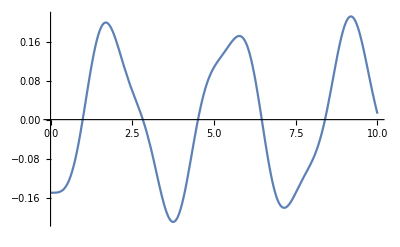

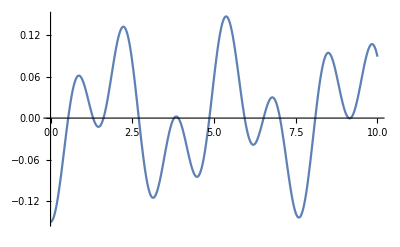

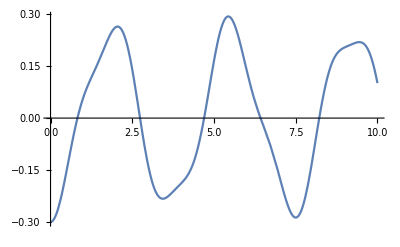

```mathematica
Plot[x1[t]/.sol2[[1]],{t,0,10}]
Plot[x2[t]/.sol2[[1]],{t,0,10}]
Plot[(x1[t]+x2[t])/.sol2[[1]],{t,0,10}]
```